```mathematica
PrimeQ[217]
```

False

```mathematica
217/7
```

31

```mathematica
√((x3-x)(x2-x)(x1-x))/.{x->(a+b x)/(c+d x)}//FullSimplify
```

√(-((a+b x-(c+d x) x1) (a+b x-(c+d x) x2) (a+b x-(c+d x) x3))/(c+d x)^3)

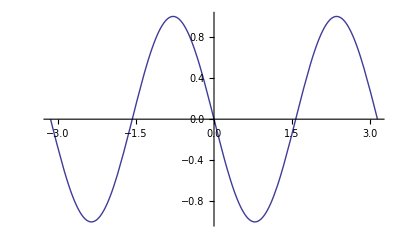

```mathematica
Plot[fr[x],{x,-π,π}]
```

```mathematica
ClearAll[xl,yl,xr,yr]
xl[t_]:=16 Sin[t]^3;
xr[t_]:=16Sin[t];
yl[t_]:=13Cos[t]-5Cos[2t]-2Cos[3t]-Cos[4t];
yr[t_]:=16Cos[t];
```

```mathematica
DiracDelta
```

```mathematica
Manipulate[ParametricPlot[{s xl[t]+(Sign[s]- s)xr[t],s yl[t]+(Sign[s]-s)yr[t]},{t,-π,π}],{s,-1,1}]
```

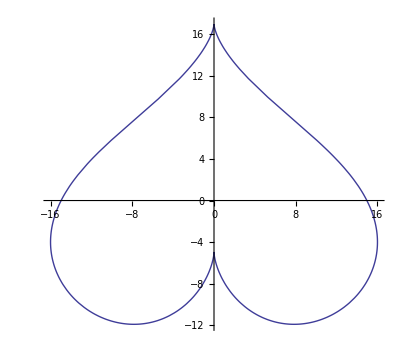

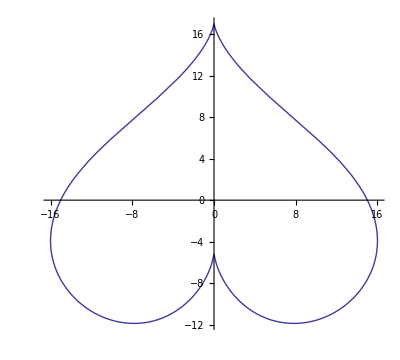

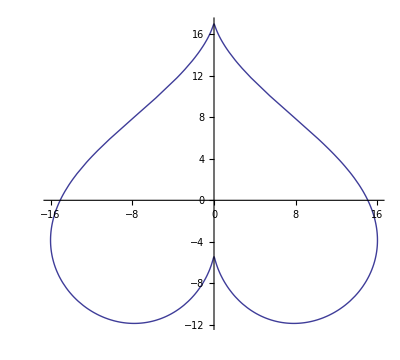

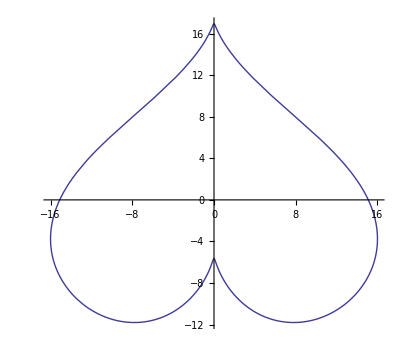

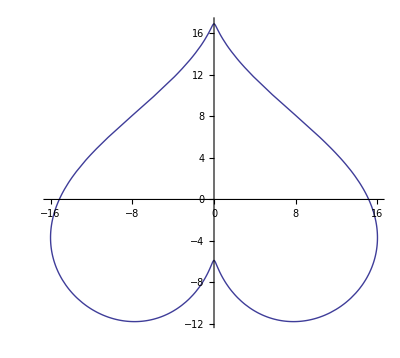

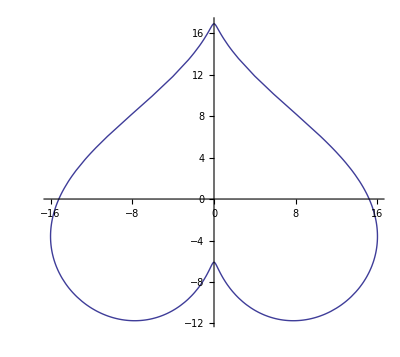

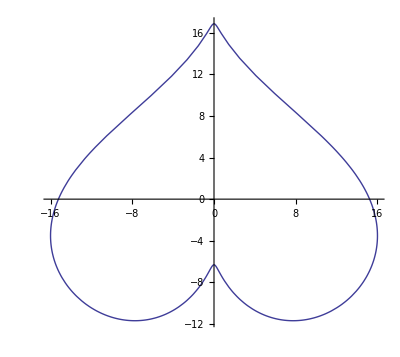

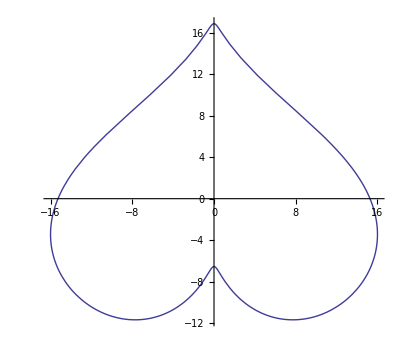

```mathematica
n=50;
Map[Print[ParametricPlot[{# xl[t]+(Sign[#]- #)xr[t],# yl[t]+(Sign[#]-#)yr[t]},{t,-π,π},Axes->False]]&,Table[i/n,{i,-n,n}]];
```